### Formato

```mathematica
(*ResourceFunction["DarkMode"][]*)
ResourceFunction["DraculaTheme"][]
```

```mathematica
style1=Style[#,16,Blue,FontWeight->Bold,Background->LightRed]&;
style3=Style[#,24,Blue,FontWeight->Bold]&;
style4=Column[#,BaseStyle->{Medium,FontFamily->"Cambria Math"}]&;
style6=Column[#,BaseStyle->{FontSize->18,FontFamily->"Cambria Math"}]&;
style5=Column[{#},BaseStyle->{Medium,FontFamily->"Cambria Math"}]&;
display[name_,value_]:=Print[style4@{name }," = ",style4@{value}]
displayunits[name_,value_,units_]:=Print[style4@{name }," = ",style4@{value},style4@{StringJoin[" [",units,"]"]}]
```

### Funciones

```mathematica
GreenTheorem[P0_,Q0_,{x_,y_}]:= Module[{P = P0,Q = Q0,F},
F = D[Q,x]- D[P,y];
Print[style1@"Equations"];
Print[style4@{"∫_C  P(x,y) ⅆx  + Q(x,y) ⅆy =  ∫_ ∫_A  ((∂Q)/(∂x) - (∂P)/(∂y)) ⅆx ⅆy"}];
Print[style4@{StringJoin[StringJoin["∫_C  ",ToString[N[P],InputForm]," ⅆx  +",ToString[N[Q],InputForm]," ⅆy"]," = ",StringJoin["∫_ ∫_A  ",ToString[F,InputForm]," ⅆx ⅆy"]]}]
]

AreaIntegralGreen[P_,Q_,x_,y_]:= Module[{dy,dx,f,F,S,K},
Clear[i];
GreenTheorem[P,Q,{x,y}];
rules = {x -> xi + (xf-xi)t,
y -> yi + (yf-yi)t,
dy -> (yf-yi),
dx ->  (xf-xi)};

(*{x,y,dy,dx}*)
f = Simplify@Expand[(P dx + Q dy)/.rules];
F = Simplify@Expand[Integrate[f,{t,0,1}]];
S=Simplify[Expand[F]];
K = FullSimplify[S]/.{xf -> x[i+1],xi-> x[i],yf -> y[i+1],yi-> y[i]};
(*K = FullSimplify[S]/.{xf -> Subscript[x, i+1],xi-> Subscript[x, i],yf -> Subscript[y, i+1],yi-> Subscript[y, i+1]};*)
Print[style1@"Summation"];
Print[style6@{StringJoin["∑",ToString[K,InputForm]]}];
S = SimplifyTermsInLoop[S];
{f,F,S}
]

SimplifyTermsInLoop[S_]:=Module[{temp,mask,nterms,terms,idxterms,subsets,isolatedterms,zeroQ,exprTeX,n},
temp = ExpandAll[S][[Range[Length[ExpandAll@S]]]];
mask = Table[(FreeQ[i,xf]&&FreeQ[i,yf])||(FreeQ[i,xi]&&FreeQ[i,yi]),{i,List@@temp}];
nterms = Length@mask;
terms = Range[nterms];
idxterms = Pick[terms,mask];
subsets = Subsets[idxterms,{2}];
Do[
isolatedterms = temp[[set]];
zeroQ = isolatedterms/.{xi->xf,yi->yf};
If[zeroQ == 0,terms = DeleteCases[terms,Alternatives@@set]]
,{set,subsets}];

Print[style1@"Factored Expression"];
Print[Simplify[temp]];

Print[style1@"Expanded Expression"];
Print[temp];
Print[style1@"Reduced Expression (trailing-leading term cancelations)"];
Print[Factor[temp[[terms]]]];
Print[style1@"TeXForm Reduced Expression"];
exprTeX = Simplify[Factor[Expand[temp[[terms]]]]]/.{xf ->Subscript[ x,i+1],xi-> Subscript[x,i],yf ->Subscript[ y,i+1],yi->Subscript[ y,i]};
Print[exprTeX];
Print[TeXForm[exprTeX]];
Factor[temp[[terms]]]]

eval[x_,i_]:=ToExpression[StringJoin[ToString[x],ToString[i]]]
xixftoTeX[exprTeX_]:=TeXForm[exprTeX/.{xf ->Subscript[ x,i+1],xi-> Subscript[x,i],yf ->Subscript[ y,i+1],yi->Subscript[ y,i]}];
```

# Derivacion de funciones

## Green’s Theorem

### Area

```mathematica
{f0,F0,S0} = AreaIntegralGreen[0,x,x,y]
```

Equations

∫_C  P(x,y) ⅆx  + Q(x,y) ⅆy =  ∫_ ∫_A  ((∂Q)/(∂x) - (∂P)/(∂y)) ⅆx ⅆy

∫_C  0. ⅆx  +x ⅆy = ∫_ ∫_A  1 ⅆx ⅆy

Summation

∑((x[i] + x[1 + i])*(-y[i] + y[1 + i]))/2

Factored Expression

1/2 (xf+xi) (yf-yi)

Expanded Expression

(xf yf)/2+(xi yf)/2-(xf yi)/2-(xi yi)/2

Reduced Expression (trailing-leading term cancelations)

1/2 (xi yf-xf yi)

TeXForm Reduced Expression

1/2 (-x_(1+i) y_i+x_i y_(1+i))

\frac{1}{2} \left(x_i y_{i+1}-x_{i+1} y_i\right)

{(t (xf-xi)+xi) (yf-yi),1/2 (xf+xi) (yf-yi),1/2 (xi yf-xf yi)}

#### Ops

```mathematica
n = 4;
MatrixForm[Table[ExpandAll[2*F0/.{xf ->eval[x,i+1],xi->eval[x,i],yf -> eval[y,i+1],yi->eval[y,i]}],{i,0,n-1}]/.{eval[x,n]->eval[x,0],eval[y,n]->eval[y,0]}]
```

(-x0 y0-x1 y0+x0 y1+x1 y1
-x1 y1-x2 y1+x1 y2+x2 y2
-x2 y2-x3 y2+x2 y3+x3 y3
x0 y0+x3 y0-x0 y3-x3 y3)

```mathematica
Clear[i]
Expand[2*S0]/.{xf -> x[i+1],xi-> x[i],yf -> y[i+1],yi-> y[i]}
i =3;
Expand[2*S0]/.{xf ->eval[x,(i+1)],xi->eval[x,(i)],yf -> eval[y,(i+1)],yi->eval[y,(i)]}
i =4;
Expand[2*S0]/.{xf ->eval[x,(i+1)],xi->eval[x,(i)],yf -> eval[y,(i+1)],yi->eval[y,(i)]}
```

-x[1+i] y[i]+x[i] y[1+i]

-x4 y3+x3 y4

-x5 y4+x4 y5

### Centroid

#### x_c

```mathematica
GreenTheorem[0,(1/2)*x^2,{x,y}]
```

Equations

∫_C  P(x,y) ⅆx  + Q(x,y) ⅆy =  ∫_ ∫_A  ((∂Q)/(∂x) - (∂P)/(∂y)) ⅆx ⅆy

∫_C  0. ⅆx  +0.5*x^2 ⅆy = ∫_ ∫_A  x ⅆx ⅆy

```mathematica
{f1,F1,S1} = AreaIntegralGreen[0,(1/2)*x^2,x,y]
```

Equations

∫_C  P(x,y) ⅆx  + Q(x,y) ⅆy =  ∫_ ∫_A  ((∂Q)/(∂x) - (∂P)/(∂y)) ⅆx ⅆy

∫_C  0. ⅆx  +0.5*x^2 ⅆy = ∫_ ∫_A  x ⅆx ⅆy

Summation

∑((x[i]^2 + x[i]*x[1 + i] + x[1 + i]^2)*(-y[i] + y[1 + i]))/6

Factored Expression

1/6 (xf^2+xf xi+xi^2) (yf-yi)

Expanded Expression

(xf^2 yf)/6+(xf xi yf)/6+(xi^2 yf)/6-(xf^2 yi)/6-(xf xi yi)/6-(xi^2 yi)/6

Reduced Expression (trailing-leading term cancelations)

-1/6 (xf+xi) (-xi yf+xf yi)

TeXForm Reduced Expression

-1/6 (x_i+x_(1+i)) (x_(1+i) y_i-x_i y_(1+i))

-\frac{1}{6} \left(x_i+x_{i+1}\right) \left(x_{i+1} y_i-x_i y_{i+1}\right)

{1/2 (t (xf-xi)+xi)^2 (yf-yi),1/6 (xf^2+xf xi+xi^2) (yf-yi),-1/6 (xf+xi) (-xi yf+xf yi)}

#### y_c

```mathematica
{f2,F2,S2} = AreaIntegralGreen[-(1/2)*y^2,0,x,y]
```

Equations

∫_C  P(x,y) ⅆx  + Q(x,y) ⅆy =  ∫_ ∫_A  ((∂Q)/(∂x) - (∂P)/(∂y)) ⅆx ⅆy

∫_C  -0.5*y^2 ⅆx  +0. ⅆy = ∫_ ∫_A  y ⅆx ⅆy

Summation

∑-1/6*((-x[i] + x[1 + i])*(y[i]^2 + y[i]*y[1 + i] + y[1 + i]^2))

Factored Expression

-1/6 (xf-xi) (yf^2+yf yi+yi^2)

Expanded Expression

-(xf yf^2)/6+(xi yf^2)/6-(xf yf yi)/6+(xi yf yi)/6-(xf yi^2)/6+(xi yi^2)/6

Reduced Expression (trailing-leading term cancelations)

1/6 (yf+yi) (xi yf-xf yi)

TeXForm Reduced Expression

1/6 (y_i+y_(1+i)) (-x_(1+i) y_i+x_i y_(1+i))

\frac{1}{6} \left(y_i+y_{i+1}\right) \left(x_i y_{i+1}-x_{i+1} y_i\right)

{-1/2 (xf-xi) (t (yf-yi)+yi)^2,-1/6 (xf-xi) (yf^2+yf yi+yi^2),1/6 (yf+yi) (xi yf-xf yi)}

#### Ops

```mathematica
ExpandAll[S2*6][[{1,2,3,4,5,6}]]
Simplify[ExpandAll[S1*6][[{2,3,4,5}]]]
```

Part::partw: Part {1,2,3,4,5,6} of xi yf^2-xf yf yi+xi yf yi-xf yi^2 does not exist.

(xi yf^2-xf yf yi+xi yf yi-xf yi^2)⟦{1,2,3,4,5,6}⟧

Part::partw: Part {2,3,4,5} of xf xi yf+xi^2 yf-xf^2 yi-xf xi yi does not exist.

(-((xf+xi) (-xi yf+xf yi)))⟦{2,3,4,5}⟧

```mathematica
n = 5
Table[ExpandAll[S2/.{xf -> x[i+1],xi-> x[i],yf -> y[i+1],yi-> y[i]}],{i,0,n-1}]/.{y[n]->y[0],x[n]->x[0]}
```

5

{-1/6 x[1] y[0]^2+1/6 x[0] y[0] y[1]-1/6 x[1] y[0] y[1]+1/6 x[0] y[1]^2,-1/6 x[2] y[1]^2+1/6 x[1] y[1] y[2]-1/6 x[2] y[1] y[2]+1/6 x[1] y[2]^2,-1/6 x[3] y[2]^2+1/6 x[2] y[2] y[3]-1/6 x[3] y[2] y[3]+1/6 x[2] y[3]^2,-1/6 x[4] y[3]^2+1/6 x[3] y[3] y[4]-1/6 x[4] y[3] y[4]+1/6 x[3] y[4]^2,1/6 x[4] y[0]^2-1/6 x[0] y[0] y[4]+1/6 x[4] y[0] y[4]-1/6 x[0] y[4]^2}

```mathematica
Factor[%149]
```

%149

### Second Moment of Area

#### I_yy

```mathematica
GreenTheorem[0,(1/3)*x^3,{x,y}]
{f3,F3,S3} = AreaIntegralGreen[0,(1/3)*x^3,x,y]
```

Equations

∫_C  P(x,y) ⅆx  + Q(x,y) ⅆy =  ∫_ ∫_A  ((∂Q)/(∂x) - (∂P)/(∂y)) ⅆx ⅆy

∫_C  0. ⅆx  +0.3333333333333333*x^3 ⅆy = ∫_ ∫_A  x^2 ⅆx ⅆy

Equations

∫_C  P(x,y) ⅆx  + Q(x,y) ⅆy =  ∫_ ∫_A  ((∂Q)/(∂x) - (∂P)/(∂y)) ⅆx ⅆy

∫_C  0. ⅆx  +0.3333333333333333*x^3 ⅆy = ∫_ ∫_A  x^2 ⅆx ⅆy

Summation

∑((x[i] + x[1 + i])*(x[i]^2 + x[1 + i]^2)*(-y[i] + y[1 + i]))/12

Factored Expression

1/12 (xf^3+xf^2 xi+xf xi^2+xi^3) (yf-yi)

Expanded Expression

(xf^3 yf)/12+1/12 xf^2 xi yf+1/12 xf xi^2 yf+(xi^3 yf)/12-(xf^3 yi)/12-1/12 xf^2 xi yi-1/12 xf xi^2 yi-(xi^3 yi)/12

Reduced Expression (trailing-leading term cancelations)

-1/12 (xf^2+xf xi+xi^2) (-xi yf+xf yi)

TeXForm Reduced Expression

-1/12 (x_i^2+x_i x_(1+i)+x_(1+i)^2) (x_(1+i) y_i-x_i y_(1+i))

-\frac{1}{12} \left(x_i^2+x_{i+1} x_i+x_{i+1}^2\right) \left(x_{i+1} y_i-x_i y_{i+1}\right)

{1/3 (t (xf-xi)+xi)^3 (yf-yi),1/12 (xf^3+xf^2 xi+xf xi^2+xi^3) (yf-yi),-1/12 (xf^2+xf xi+xi^2) (-xi yf+xf yi)}

#### I_xx

```mathematica
GreenTheorem[-(1/3)*y^3,0,{x,y}]
{f4,F4,S4} = AreaIntegralGreen[-(1/3)*y^3,0,x,y]
```

Equations

∫_C  P(x,y) ⅆx  + Q(x,y) ⅆy =  ∫_ ∫_A  ((∂Q)/(∂x) - (∂P)/(∂y)) ⅆx ⅆy

∫_C  -0.3333333333333333*y^3 ⅆx  +0. ⅆy = ∫_ ∫_A  y^2 ⅆx ⅆy

Equations

∫_C  P(x,y) ⅆx  + Q(x,y) ⅆy =  ∫_ ∫_A  ((∂Q)/(∂x) - (∂P)/(∂y)) ⅆx ⅆy

∫_C  -0.3333333333333333*y^3 ⅆx  +0. ⅆy = ∫_ ∫_A  y^2 ⅆx ⅆy

Summation

∑-1/12*((-x[i] + x[1 + i])*(y[i] + y[1 + i])*(y[i]^2 + y[1 + i]^2))

Factored Expression

-1/12 (xf-xi) (yf^3+yf^2 yi+yf yi^2+yi^3)

Expanded Expression

-(xf yf^3)/12+(xi yf^3)/12-1/12 xf yf^2 yi+1/12 xi yf^2 yi-1/12 xf yf yi^2+1/12 xi yf yi^2-(xf yi^3)/12+(xi yi^3)/12

Reduced Expression (trailing-leading term cancelations)

1/12 (xi yf-xf yi) (yf^2+yf yi+yi^2)

TeXForm Reduced Expression

1/12 (-x_(1+i) y_i+x_i y_(1+i)) (y_i^2+y_i y_(1+i)+y_(1+i)^2)

\frac{1}{12} \left(y_i^2+y_{i+1} y_i+y_{i+1}^2\right) \left(x_i y_{i+1}-x_{i+1} y_i\right)

{-1/3 (xf-xi) (t (yf-yi)+yi)^3,-1/12 (xf-xi) (yf^3+yf^2 yi+yf yi^2+yi^3),1/12 (xi yf-xf yi) (yf^2+yf yi+yi^2)}

#### Ops

```mathematica
SS3 = SimplifyTermsInLoop[S3];
ExpandAll[SS3]
```

Factored Expression

-1/12 (xf^2+xf xi+xi^2) (-xi yf+xf yi)

Expanded Expression

1/12 xf^2 xi yf+1/12 xf xi^2 yf+(xi^3 yf)/12-(xf^3 yi)/12-1/12 xf^2 xi yi-1/12 xf xi^2 yi

Reduced Expression (trailing-leading term cancelations)

-1/12 (xf^2+xf xi+xi^2) (-xi yf+xf yi)

TeXForm Reduced Expression

-1/12 (x_i^2+x_i x_(1+i)+x_(1+i)^2) (x_(1+i) y_i-x_i y_(1+i))

-\frac{1}{12} \left(x_i^2+x_{i+1} x_i+x_{i+1}^2\right) \left(x_{i+1} y_i-x_i y_{i+1}\right)

1/12 xf^2 xi yf+1/12 xf xi^2 yf+(xi^3 yf)/12-(xf^3 yi)/12-1/12 xf^2 xi yi-1/12 xf xi^2 yi

#### I_xy

```mathematica
{f5,F5,S5} = AreaIntegralGreen[0, (x^2*y)/2,x,y]
```

Equations

∫_C  P(x,y) ⅆx  + Q(x,y) ⅆy =  ∫_ ∫_A  ((∂Q)/(∂x) - (∂P)/(∂y)) ⅆx ⅆy

∫_C  0. ⅆx  +0.5*x^2*y ⅆy = ∫_ ∫_A  x*y ⅆx ⅆy

Summation

∑((-y[i] + y[1 + i])*(2*x[i]*x[1 + i]*(y[i] + y[1 + i]) + x[i]^2*(3*y[i] + y[1 + i]) + x[1 + i]^2*(y[i] + 3*y[1 + i])))/24

Factored Expression

1/24 (yf-yi) (2 xf xi (yf+yi)+xf^2 (3 yf+yi)+xi^2 (yf+3 yi))

Expanded Expression

(xf^2 yf^2)/8+1/12 xf xi yf^2+(xi^2 yf^2)/24-1/12 xf^2 yf yi+1/12 xi^2 yf yi-(xf^2 yi^2)/24-1/12 xf xi yi^2-(xi^2 yi^2)/8

Reduced Expression (trailing-leading term cancelations)

-1/24 (-xi yf+xf yi) (2 xf yf+xi yf+xf yi+2 xi yi)

TeXForm Reduced Expression

1/24 (-x_(1+i) y_i+x_i y_(1+i)) (x_i (2 y_i+y_(1+i))+x_(1+i) (y_i+2 y_(1+i)))

\frac{1}{24} \left(x_i y_{i+1}-x_{i+1} y_i\right) \left(x_i \left(2 y_i+y_{i+1}\right)+x_{i+1} \left(y_i+2 y_{i+1}\right)\right)

{1/2 (t (xf-xi)+xi)^2 (yf-yi) (t (yf-yi)+yi),1/24 (yf-yi) (2 xf xi (yf+yi)+xf^2 (3 yf+yi)+xi^2 (yf+3 yi)),-1/24 (-xi yf+xf yi) (2 xf yf+xi yf+xf yi+2 xi yi)}

```mathematica
Factor[Expand[S5]]
```

-1/24 (-xi yf+xf yi) (2 xf yf+xi yf+xf yi+2 xi yi)

#### Jz

```mathematica
S3
S4
Factor[S3+S4]
xixftoTeX[Factor[S3+S4]]
```

-1/12 (xf^2+xf xi+xi^2) (-xi yf+xf yi)

1/12 (xi yf-xf yi) (yf^2+yf yi+yi^2)

-1/12 (-xi yf+xf yi) (xf^2+xf xi+xi^2+yf^2+yf yi+yi^2)

-\frac{1}{12} \left(x_{i+1} y_i-x_i y_{i+1}\right) \left(x_i^2+x_{i+1} x_i+x_{i+1}^2+y_i^2+y_{i+1}^2+y_i y_{i+1}\right)

```mathematica
texsusbscripts = {xf ->Subscript[ x,i+1],xi-> Subscript[x,i],yf ->Subscript[ y,i+1],yi->Subscript[ y,i]};
symS4 = Factor[Expand[S4]]/.texsusbscripts
TeXForm[symS4]
```

1/12 (-x_(1+i) y_i+x_i y_(1+i)) (y_i^2+y_i y_(1+i)+y_(1+i)^2)

\frac{1}{12} \left(y_i^2+y_{i+1} y_i+y_{i+1}^2\right) \left(x_i y_{i+1}-x_{i+1} y_i\right)

### Second Moment of Area for a Thin Shell

```mathematica
rules = {x -> xi + (xf-xi)t,
y -> yi + (yf-yi)t,
dy -> (yf-yi),
dx ->  (xf-xi)};
```

#### Area

```mathematica
AreaShell = τ √((dx)^2+(dy)^2)
Integrate[AreaShell/.rules,{t,0,1}]
```

√(dx^2+dy^2) τ

√((xf-xi)^2+(yf-yi)^2) τ

#### Centroid

```mathematica
xShell =x τ √((dx)^2+(dy)^2)
xIShell = Integrate[xShell/.rules,{t,0,1}]
xixftoTeX[xIShell]

yShell =y τ √((dx)^2+(dy)^2)
Integrate[yShell/.rules,{t,0,1}]
```

√(dx^2+dy^2) x τ

1/2 (xf+xi) √((xf-xi)^2+(yf-yi)^2) τ

√(dx^2+dy^2) y τ

1/2 √((xf-xi)^2+(yf-yi)^2) (yf+yi) τ

\frac{1}{2} \tau  \left(x_i+x_{i+1}\right) \sqrt{\left(x_{i+1}-x_i\right){}^2+\left(y_{i+1}-y_i\right){}^2}

#### Ixx

```mathematica
ShellIxx = y^2 τ √((dx)^2+(dy)^2)
IShellIxx= Integrate[ShellIxx/.rules,{t,0,1}]
xixftoTeX[IShellIxx]
```

√(dx^2+dy^2) y^2 τ

1/3 √((xf-xi)^2+(yf-yi)^2) (yf^2+yf yi+yi^2) τ

\frac{1}{3} \tau  \left(y_i^2+y_{i+1} y_i+y_{i+1}^2\right) \sqrt{\left(x_{i+1}-x_i\right){}^2+\left(y_{i+1}-y_i\right){}^2}

#### Iyy

```mathematica
ShellIyy = x^2 τ √((dx)^2+(dy)^2)
IShellIyy=Integrate[ShellIyy/.rules,{t,0,1}]
xixftoTeX[IShellIyy]
```

√(dx^2+dy^2) x^2 τ

1/3 (xf^2+xf xi+xi^2) √((xf-xi)^2+(yf-yi)^2) τ

\frac{1}{3} \tau  \left(x_i^2+x_{i+1} x_i+x_{i+1}^2\right) \sqrt{\left(x_{i+1}-x_i\right){}^2+\left(y_{i+1}-y_i\right){}^2}

#### Ixy

```mathematica
ShellIxy = x y τ √((dx)^2+(dy)^2)
IShellIxy=Integrate[ShellIxy/.rules,{t,0,1}];
Factor[Expand@IShellIxy]
xixftoTeX[Factor[Expand@IShellIxy]]
```

√(dx^2+dy^2) x y τ

1/6 √((xf-xi)^2+(yf-yi)^2) (2 xf yf+xi yf+xf yi+2 xi yi) τ

\frac{1}{6} \tau  \left(2 x_i y_i+x_{i+1} y_i+x_i y_{i+1}+2 x_{i+1} y_{i+1}\right) \sqrt{\left(x_{i+1}-x_i\right){}^2+\left(y_{i+1}-y_i\right){}^2}

## Experimentos PDE

```mathematica
pde=D[Q[x,y],x]- D[P[x,y],y]==x
```

-P^(0,1)[x,y]+Q^(1,0)[x,y]==x

```mathematica
soln=DSolve[pde/.{D[P[x,y],y]->0},Q[x,y],{x,y}]
sol1=DSolve[pde,P[x,y],{x,y}]
```

{{Q[x,y]→x^2/2+C[1][y]}}

{{P[x,y]→C[1][x]+(-x+Q^(1,0)[x,K[1]])K[1]1y}}

```mathematica
Q1[x_,y_]=Q[x,y]/. soln[[1]]
```

x^2/2+C[1][y]

```mathematica
Q1[x,0]
```

x^2/2+C[1][0]

```mathematica
Integrate[x,y]
```

x y

```mathematica
GreenTheorem[-Integrate[x,y]/2,Integrate[x,x]/2,{x,y}]
```

Equations

∫_C  P(x,y) ⅆx  + Q(x,y) ⅆy =  ∫_ ∫_A  ((∂Q)/(∂x) - (∂P)/(∂y)) ⅆx ⅆy

∫_C  -0.5*x*y ⅆx  +0.25*x^2 ⅆy = ∫_ ∫_A  x ⅆx ⅆy

```mathematica
AreaIntegralGreen[-Integrate[x,y]/2,Integrate[x,x]/2,x,y]
```

Equations

∫_C  P(x,y) ⅆx  + Q(x,y) ⅆy =  ∫_ ∫_A  ((∂Q)/(∂x) - (∂P)/(∂y)) ⅆx ⅆy

∫_C  -0.5*x*y ⅆx  +0.25*x^2 ⅆy = ∫_ ∫_A  x ⅆx ⅆy

Summation

∑(2*x[i]*x[1 + i]*(-y[i] + y[1 + i]) - x[1 + i]^2*(2*y[i] + y[1 + i]) + x[i]^2*(y[i] + 2*y[1 + i]))/12

Factored Expression

1/12 (2 xf xi (yf-yi)+xi^2 (2 yf+yi)-xf^2 (yf+2 yi))

Expanded Expression

-(xf^2 yf)/12+(xf xi yf)/6+(xi^2 yf)/6-(xf^2 yi)/6-(xf xi yi)/6+(xi^2 yi)/12

Reduced Expression (trailing-leading term cancelations)

-1/6 (xf+xi) (-xi yf+xf yi)

TeXForm Reduced Expression

-1/6 (x_i+x_(1+i)) (x_(1+i) y_i-x_i y_(1+i))

-\frac{1}{6} \left(x_i+x_{i+1}\right) \left(x_{i+1} y_i-x_i y_{i+1}\right)

{-1/4 (t (xf-xi)+xi) (t (xf-xi) (yf-yi)+2 xf yi-xi (yf+yi)),1/12 (2 xf xi (yf-yi)+xi^2 (2 yf+yi)-xf^2 (yf+2 yi)),-1/6 (xf+xi) (-xi yf+xf yi)}

```mathematica
GreenTheoremSuggestion[f_,{x_,y_}]:= Module[{P ,Q ,F,solc1,solc2},
Clear[c1];
Clear[c2];
Q = Integrate[f,x];

P = -Integrate[f,y];
F = c1 D[Q,x]- c2 D[P,y];
solc1 = Solve[F==f,{c1}];
solc2 = Solve[F==f,{c2}];

Print[style4@{"∫_C  P(x,y) ⅆx  + Q(x,y) ⅆy =  ∫_ ∫_A  ((∂Q)/(∂x) - (∂P)/(∂y)) ⅆx ⅆy"}];
Print[style1@"Solution 1"];
Print[style4@{StringJoin["P(x,y) = " ,ToString[0,InputForm], ",   Q(x,y) = ", ToString[Q,InputForm]]}];
Print[style1@"Solution 2"];
Print[style4@{StringJoin["P(x,y) = " ,ToString[P,InputForm], ",   Q(x,y) = ", ToString[0,InputForm]]}];
Print[style1@"Solution 3"];
Print[style4@{StringJoin["P(x,y) = " ,ToString[c2*P/.solc2,InputForm], ",   Q(x,y) = ", ToString[c1*Q,InputForm]]}];
Print[style1@"Solution 4"];
Print[style4@{StringJoin["P(x,y) = " ,ToString[c2*P,InputForm], ",   Q(x,y) = ", ToString[c1*Q/.solc1,InputForm]]}];


{P,Q,F}
]
```

```mathematica
GreenTheoremSuggestion[x y,{x,y}]
```

∫_C  P(x,y) ⅆx  + Q(x,y) ⅆy =  ∫_ ∫_A  ((∂Q)/(∂x) - (∂P)/(∂y)) ⅆx ⅆy

Solution 1

P(x,y) = 0,   Q(x,y) = (x^2*y)/2

Solution 2

P(x,y) = -1/2*(x*y^2),   Q(x,y) = 0

Solution 3

P(x,y) = {-1/2*((1 - c1)*x*y^2)},   Q(x,y) = (c1*x^2*y)/2

Solution 4

P(x,y) = -1/2*(c2*x*y^2),   Q(x,y) = {((1 - c2)*x^2*y)/2}

{-(x y^2)/2,(x^2 y)/2,c1 x y+c2 x y}

```mathematica
rules = {x -> xi + (xf-xi)t,
y -> yi + (yf-yi)t,
dy -> (yf-yi),
dx ->  (xf-xi)};
```

```mathematica
Integrate[y^2 √(dx^2+dy^2)/.rules,{t,0,1}]
```

1/3 √((xf-xi)^2+(yf-yi)^2) (yf^2+yf yi+yi^2)

```mathematica
Manipulate[Column[{Plot3D[Subscript[f,1],{x,1,5},{y,1,1.05 C},Sequence[MeshFunctions->{Apply[Function,{{x,y,z},z-ReplaceAll[Subscript[f,1],y->C]}]},MeshStyle->Directive[Thickness[0.005],Red],Mesh->{{0}},ImageSize->250,AxesLabel->{"x","y","u(x, y)"}]],Framed[Text[StringForm["The behavior of the solution u(x, y) = `1` over the curves y = C",Subscript[f,1]]],Background->Lighter[Gray,0.9],FrameStyle->None]}],{Subscript[f,1],{y,y^2,y/(y+1),E^y}},{{C,2},2,6},Sequence[ControlPlacement->{Top,Top},SaveDefinitions->True]]
```

```mathematica
DSolve[D[u[x,y], {x}] + y D[u[x,y], {y}] == 0, 
 u[x, y], {x, y}, GeneratedParameters -> (Subscript[f, #1] &)]
```

{{u[x,y]→f_1[ⅇ^-x y]}}

```mathematica
DSolve[(D[u[x,y], {y}] -D[u[x,y], {x}])w2 + (D[u[x,y], {x}] -D[u[x,y], {y}])w3 == x, 
 u[x, y], {x, y}, GeneratedParameters -> (Subscript[f, #1] &)]
```

{{u[x,y]→-x^2/(2 (w2-w3))+f_1[x+y]}}

```mathematica
DSolve[{(D[u3[x,y,z], {y}] -D[u2[x,y,z], {z}])*0*w1+(D[u1[x,y,z], {z}] -D[u3[x,y,z], {x}])w2 + (D[u2[x,y,z], {x}] -D[u1[x,y,z], {y}])w3 == 1,u1[x,y,z]==0}, 
{ u1[x,y,z],u2[x,y,z],u3[x,y,z]}, {x, y,z}, GeneratedParameters -> (Subscript[f, #1] &)]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[{w3 (-u1^(0,1,0)[x,y,z]+u2^(1,0,0)[x,y,z])+w2 (u1^(0,0,1)[x,y,z]-u3^(1,0,0)[x,y,z])==1,u1[x,y,z]==0},{u1[x,y,z],u2[x,y,z],u3[x,y,z]},{x,y,z},GeneratedParameters→(f_#1&)]

```mathematica
DSolve[{(-D[u3[x,y,z], {x}]) + (D[u2[x,y,z], {x}] ) == 1}, 
{ u2[x,y,z],u3[x,y,z]}, {x, y,z}, GeneratedParameters -> (Subscript[f, #1] &)]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[{u2^(1,0,0)[x,y,z]-u3^(1,0,0)[x,y,z]==1},{u2[x,y,z],u3[x,y,z]},{x,y,z},GeneratedParameters→(f_#1&)]

## Stokes Theorem

### Funciones

```mathematica
(*Rotación en X*)
-Graphics-;
Rx[γ_]:=({{1, 0, 0}, {0, Cos[γ], -Sin[γ]}, {0, Sin[γ], Cos[γ]}});
(*Rotación en Y*)
-Graphics-;
Ry[β_]:=({{Cos[β], 0, Sin[β]}, {0, 1, 0}, {-Sin[β], 0, Cos[β]}});
(*Rotación en Z*)
-Graphics-;
Rz[α_]:=({{Cos[α], -Sin[α], 0}, {Sin[α], Cos[α], 0}, {0, 0, 1}});
Rz[θ12]//MatrixForm
INTG[Ixx_]:=Simplify[Integrate[Expand[Ixx],{t,0,1}]]
```

(Cos[θ12] | -Sin[θ12] | 0
Sin[θ12] | Cos[θ12] | 0
0 | 0 | 1)

```mathematica
refframe[PB_,CAB_,arrowLength_] := Map[{Apply[RGBColor, #],Arrow[Tube[{PB,PB+ arrowLength (CAB.#)}]]} &,
  IdentityMatrix[3]]
TR[Rz_,X0_]:=Dot[Rz,#]&@X0
```

```mathematica
X0 = IdentityMatrix[3]
x0 = TR[Ry[β],TR[Rx[γ],TR[Rz[α],X0]]];
x0//MatrixForm
```

{{1,0,0},{0,1,0},{0,0,1}}

(Cos[α] Cos[β]+Sin[α] Sin[β] Sin[γ] | -Cos[β] Sin[α]+Cos[α] Sin[β] Sin[γ] | Cos[γ] Sin[β]
Cos[γ] Sin[α] | Cos[α] Cos[γ] | -Sin[γ]
-Cos[α] Sin[β]+Cos[β] Sin[α] Sin[γ] | Sin[α] Sin[β]+Cos[α] Cos[β] Sin[γ] | Cos[β] Cos[γ])

```mathematica
TR[Rz[α],X0]//MatrixForm
Table[Rz[α].ei,{ei,X0}]//MatrixForm
```

(Cos[α] | -Sin[α] | 0
Sin[α] | Cos[α] | 0
0 | 0 | 1)

(Cos[α] | Sin[α] | 0
-Sin[α] | Cos[α] | 0
0 | 0 | 1)

```mathematica
Rz[α].{1,0,0}
Rz[α].{0,1,0}
Rz[α].Rx[γ].{0,0,1}//MatrixForm
```

{Cos[α],Sin[α],0}

{-Sin[α],Cos[α],0}

(Sin[α] Sin[γ]
-Cos[α] Sin[γ]
Cos[γ])

```mathematica
(Rx[γ].(Rz[α].{0,0,1}))//MatrixForm

Rz[α].Rx[β].{0,0,1}
C1 = Table[Rz[α].Rx[β].ei,{ei,X0}]
```

(0
-Sin[γ]
Cos[γ])

{Sin[α] Sin[β],-Cos[α] Sin[β],Cos[β]}

{{Cos[α],Sin[α],0},{-Cos[β] Sin[α],Cos[α] Cos[β],Sin[β]},{Sin[α] Sin[β],-Cos[α] Sin[β],Cos[β]}}

```mathematica
C1//MatrixForm
Rz[α].Rx[β]//MatrixForm
```

(Cos[α] | Sin[α] | 0
-Cos[β] Sin[α] | Cos[α] Cos[β] | Sin[β]
Sin[α] Sin[β] | -Cos[α] Sin[β] | Cos[β])

(Cos[α] | -Cos[β] Sin[α] | Sin[α] Sin[β]
Sin[α] | Cos[α] Cos[β] | -Cos[α] Sin[β]
0 | Sin[β] | Cos[β])

```mathematica
Manipulate[Graphics3D[{refframe[{0,0,0},X0,1],refframe[{0.1,0.1,0.1},C1ᵀ,0.501],refframe[{0.15,0.15,0.15},Rz[α].Rx[β],0.450]},ViewPoint->{-3,2.5,2.5},ViewVertical->{0,1,0},Boxed->False,AxesOrigin->{0,0,0},PlotRange->{{-.5,1.0},{-.5,1.0},{-.5,1.0}}]/.{α->a,β->b},{{a,0},-π,π},{{b,0},-π,π}]
```

```mathematica
Rx[β].(Rz[α].{0,0,1})
```

{0,-Sin[β],Cos[β]}

```mathematica
Clear[pi,pf,r,dr]
```

```mathematica
rules3D ={
 x -> xi + (xf-xi)t,
y -> yi + (yf-yi)t,
z -> zi + (zf-zi)t,
r -> pi + (pf-pi)t,
dr -> pf-pi,
pi -> {xi,yi,zi},
pf -> {xf,yf,zf}}

F ={0,x Cos[γ],x Sin[γ]}
```

{x→t (xf-xi)+xi,y→t (yf-yi)+yi,z→t (zf-zi)+zi,r→pi+(pf-pi) t,dr→pf-pi,pi→{xi,yi,zi},pf→{xf,yf,zf}}

{0,x Cos[γ],x Sin[γ]}

```mathematica
iF = F/.rules3D
idr=dr/.rules3D/.rules3D
Integrate[iF.idr,{t,0,1}]
```

{0,(t (xf-xi)+xi) Cos[γ],(t (xf-xi)+xi) Sin[γ]}

{xf-xi,yf-yi,zf-zi}

1/2 (xf+xi) ((yf-yi) Cos[γ]+(zf-zi) Sin[γ])

```mathematica
w = Ry[β].(Rx[γ].(Rz[α].{0,0,1}))
TeXForm[w]
```

{Cos[γ] Sin[β],-Sin[γ],Cos[β] Cos[γ]}

\{\sin (\beta ) \cos (\gamma ),-\sin (\gamma ),\cos (\beta ) \cos (\gamma )\}

```mathematica
Curl[{Fx[x,y,z],Fy[x,y,z],Fz[x,y,z]},{x,y,z}]
```

{-Fy^(0,0,1)[x,y,z]+Fz^(0,1,0)[x,y,z],Fx^(0,0,1)[x,y,z]-Fz^(1,0,0)[x,y,z],-Fx^(0,1,0)[x,y,z]+Fy^(1,0,0)[x,y,z]}

```mathematica
iF = {0,w3 x,- w2 x +w1 y}/.rules3D
idr=dr/.rules3D/.rules3D
Integrate[iF.idr,{t,0,1}]
```

{0,w3 (t (xf-xi)+xi),-w2 (t (xf-xi)+xi)+w1 (t (yf-yi)+yi)}

{xf-xi,yf-yi,zf-zi}

1/2 (w3 (xf+xi) (yf-yi)-(w2 (xf+xi)-w1 (yf+yi)) (zf-zi))

```mathematica
D[(x z)/(w3 z - w2 y),z]
```

-(w3 x z)/(-w2 y+w3 z)^2+x/(-w2 y+w3 z)

```mathematica
D[(x y)/(w3 z - w2 y),y]
```

(w2 x y)/(-w2 y+w3 z)^2+x/(-w2 y+w3 z)

```mathematica
foil = {{6.226712510817800084*10^-01,-5.859535510249033741*10^-02},{5.978572118925907786*10^-01,-4.933639158897681898*10^-02},{5.652320024331314308*10^-01,-3.653947402140925865*10^-02},{5.280176416223206770*10^-01,-2.152869158897682822*10^-02},{4.882068672979962831*10^-01,-6.392336183571419549*10^-03},{4.460005416223206121*10^-01,8.369234086698845720*10^-03},{4.020278375682665439*10^-01,2.283197192453668631*10^-02},{3.577284983790773865*10^-01,3.663776246507723100*10^-02},{3.138848078385368390*10^-01,4.934259354615830317*10^-02},{2.705559497304287353*10^-01,6.077578138399614832*10^-02},{2.276714483790773513*10^-01,7.088102868129345091*10^-02},{1.852338024331314226*10^-01,7.960101246507722550*10^-02},{1.432423591898882020*10^-01,8.686790705967183113*10^-02},{1.015944402709692690*10^-01,9.262498408669884997*10^-02},{6.007530243313146529*10^-02,9.688998003264479020*10^-02},{1.882545378448278323*10^-02,9.973507327588804205*10^-02},{-2.140561108038206706*10^-02,1.011737719245366790*10^-01},{-5.991943540470646284*10^-02,1.010441570596718325*10^-01},{-9.655938945876045565*10^-02,9.923011516777993646*10^-02},{-1.312926110803820101*10^-01,9.569017057318535135*10^-02},{-1.641351354047063948*10^-01,9.040857462723939086*10^-02},{-1.951465651344361507*10^-01,8.338757327588804114*10^-02},{-2.243531786479496248*10^-01,7.508033949210426994*10^-02},{-2.503546799993009442*10^-01,6.668156922183400559*10^-02},{-2.720578840533550702*10^-01,5.806261787048264122*10^-02},{-2.903529448641659072*10^-01,4.825758408669884175*10^-02},{-3.063780624317334333*10^-01,3.741915300561778068*10^-02},{-3.204256664857874637*10^-01,2.663119084345564463*10^-02},{-3.322430245938955973*10^-01,1.611116111372589560*10^-02},{-3.420153502695713055*10^-01,5.860021924536680700*10^-03},{-3.501306678371388648*10^-01,-3.868576724111945624*10^-03},{-3.568998110803821011*10^-01,-1.289156456194977089*10^-02},{-3.625262867560577473*10^-01,-2.118092267005789592*10^-02},{-3.671670867560578033*10^-01,-2.880475375113898673*10^-02},{-3.709284948641659030*10^-01,-3.586008212951737745*10^-02},{-3.738192178371388397*10^-01,-4.248079023762545148*10^-02},{-3.758452327020037065*10^-01,-4.875658483222005540*10^-02},{-3.770111989182199363*10^-01,-5.473140510249033946*10^-02},{-3.773275408101118278*10^-01,-6.039032537276058099*10^-02},{-3.767826002695712773*10^-01,-6.600923212951734231*10^-02},{-3.752978056749767255*10^-01,-7.163809023762546246*10^-02},{-3.728307637830848287*10^-01,-7.713594969708494065*10^-02},{-3.692674705398415469*10^-01,-8.229345510249033713*10^-02},{-3.643992272965983492*10^-01,-8.672981185924706626*10^-02},{-3.580542272965983597*10^-01,-8.987984158897682763*10^-02},{-3.504322759452470071*10^-01,-9.194090104843627431*10^-02},{-3.416014759452470351*10^-01,-9.367209294032817490*10^-02},{-3.312867664857875316*10^-01,-9.521277267005789913*10^-02},{-3.189957218911929626*10^-01,-9.653726050789573909*10^-02},{-3.039768867560578292*10^-01,-9.768086456194978451*10^-02},{-2.851682218911928968*10^-01,-9.882621996735520276*10^-02},{-2.615583056749768431*10^-01,-1.003374686160038443*10^-01},{-2.331724002695713671*10^-01,-1.020951388862741255*10^-01},{-2.016033327020037569*10^-01,-1.029833199673551997*10^-01},{-1.678005894587606961*10^-01,-1.021319551024903460*10^-01},{-1.315544570263282032*10^-01,-9.914790375113900767*10^-02},{-9.202111918849031902*10^-02,-9.407068212951738562*10^-02},{-4.877970702632808409*10^-02,-8.722892131870656207*10^-02},{-2.560721891192867077*10^-03,-7.909213618357141540*10^-02},{4.557052270340147121*10^-02,-7.013639834573362486*10^-02},{9.375018621691505460*10^-02,-6.080987942681469194*10^-02},{1.409207402709691803*10^-01,-5.115779699438223471*10^-02},{1.862173267574555036*10^-01,-4.181927402140931532*10^-02},{2.283792145952933672*10^-01,-3.410636726465253454*10^-02},{2.683565862169150495*10^-01,-2.837565510249035264*10^-02},{3.068712848655635317*10^-01,-2.450423077816603692*10^-02},{3.438304997304287292*10^-01,-2.243493888627412156*10^-02},{3.790062483790772041*10^-01,-2.231350239978762903*10^-02},{4.128858294601585599*10^-01,-2.439725780519305318*10^-02},{4.467875267574556997*10^-01,-2.907358753492276029*10^-02},{4.826853159466446552*10^-01,-3.640724429167947057*10^-02},{5.215357727034016788*10^-01,-4.594591726465251796*10^-02},{5.612420943250231442*10^-01,-5.623759023762543718*10^-02},{5.965907510817797244*10^-01,-6.545285915654432130*10^-02},{6.226712510817800084*10^-01,-7.222535510249034063*10^-02}};
```

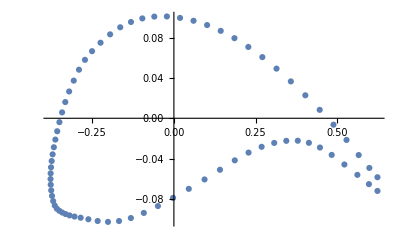

```mathematica
ListPlot[foil]
```

```mathematica
n = Length[foil];
foil3D = Append[foilᵀ,ConstantArray[0,n]]ᵀ;
foil3D1 = Append[foilᵀ,ConstantArray[0.5,n]]ᵀ;
ListLinePlot3D[{foil3D,foil3D1},ViewVertical->{0, 1, 0}]
Graphics3D[Polygon[foil3D]]
```

-Graphics3D-

-Graphics3D-

```mathematica
gpos = {0.4,-0.05,0.4};
scale = {-0.5,1.25};
rotatedairfoil = Dot[Rx[β].Rz[α],#]&/@foil3D ;
rotatedairfoil = (rotatedairfoilᵀ + gpos)ᵀ;

rotatedairfoil2 = Dot[Rx[β].Rz[α],#]&/@foil3D ;
rotatedairfoil2 = (rotatedairfoil2ᵀ + 2*gpos)ᵀ;

Manipulate[Show[Graphics3D[{refframe[{0,0,0},X0,0.35],refframe[gpos,Rx[β].Rz[α],0.35],Polygon[foil3D],Polygon[rotatedairfoil], Polygon[rotatedairfoil2]},ViewPoint->{-3,2.5,2.5},ViewVertical->{0,1,0},Boxed->False,AxesOrigin->{0,0,0},PlotRange->{scale,scale,scale}]/.{α->a,β->b},ListLinePlot3D[{foil3D,rotatedairfoil/.{α->a,β->b}}]],{{a,0},-π,π},{{b,0},-π,π}]
```

ListLinePlot3D::ldata: 
   {foil3D, rotatedairfoil} is not a valid dataset or list of datasets.

PlotRange::prng: 
   Value of option PlotRange -> {scale, scale, scale}
     is not All, Full, Automatic, a positive machine number, or an appropriate
     list of range specifications.

Show::gcomb: Could not combine the graphics objects in 
    Show[-Graphics3D-, ListLinePlot3D[{foil3D, rotatedairfoil}]].

```mathematica
Integrate
```

```mathematica
Integrate[1, {x, 0, 1}, {y, 0, 1 - x}, {z, 0, 1 - x - y}]
```

1/6

```mathematica
{x->ϵ, y->η,z-> ζ}
```

```mathematica
TetrahedronTransform={x1 + (x2 - x1)* ϵ + (x3-x1) *η+ (x4-x1)*ζ, y1 + (y2 - y1)* ϵ + (y3-y1) *η+ (y4-y1)*ζ, z1 + (z2 - z1)* ϵ + (z3-z1) *η+ (z4-z1)*ζ}

Integrate[1, {x, 0, 1}, {y, 0, 1 - x}, {z, 0, 1 - x - y}]
```

{x1+(-x1+x2) ϵ+(-x1+x4) ζ+(-x1+x3) η,y1+(-y1+y2) ϵ+(-y1+y4) ζ+(-y1+y3) η,z1+(-z1+z2) ϵ+(-z1+z4) ζ+(-z1+z3) η}

1/6

```mathematica
Integrate[1, {x, 0, 1}, {y, 0, 1 - x}, {z, 0, 1}]
```

1/2

```mathematica
coordTransform[pt_List,transform_,var_:Automatic]:=Module[{v,f},v=If[var===Automatic,Variables[Level[transform,{-1}]],var];
f=Function@@{v,transform};
f@@pt]
```

```mathematica
coordTransform[{0,0,1},TetrahedronTransform,{ϵ, η, ζ}]
```

{x4,y4,z4}

```mathematica
D[TetrahedronTransform,{{ϵ, η, ζ}}]//MatrixForm
```

(-x1+x2 | -x1+x3 | -x1+x4
-y1+y2 | -y1+y3 | -y1+y4
-z1+z2 | -z1+z3 | -z1+z4)

```mathematica
TetrahedronTransformVar={x->x1 + (x2 - x1)* ϵ + (x3-x1) *η+ (x4-x1)*ζ, y->y1 + (y2 - y1)* ϵ + (y3-y1) *η+ (y4-y1)*ζ, z->z1 + (z2 - z1)* ϵ + (z3-z1) *η+ (z4-z1)*ζ}
```

{x→x1+(-x1+x2) ϵ+(-x1+x4) ζ+(-x1+x3) η,y→y1+(-y1+y2) ϵ+(-y1+y4) ζ+(-y1+y3) η,z→z1+(-z1+z2) ϵ+(-z1+z4) ζ+(-z1+z3) η}

```mathematica
Integrate[(y^2)/.TetrahedronTransformVar, {ϵ, 0, 1}, {η, 0, 1 - ϵ}, {ζ, 0, t}]
```

1/12 t ((1-2 t+2 t^2) y1^2+y2^2+y3^2+2 t y3 y4+2 t^2 y4^2+y2 (y3+2 t y4)-(-1+2 t) y1 (y2+y3+2 t y4))

```mathematica
(y^2+z^2)/.TetrahedronTransformVar
```

(y1+(-y1+y2) ϵ+(-y1+y4) ζ+(-y1+y3) η)^2+(z1+(-z1+z2) ϵ+(-z1+z4) ζ+(-z1+z3) η)^2

```mathematica
2^2
```

4

```mathematica
Simplify@Expand[Integrate[(y^2)/.TetrahedronTransformVar, {ϵ, 0, 1}, {η, 0, 1 - ϵ}, {ζ, 0, t}]]
```

1/12 t ((1-2 t+2 t^2) y1^2+y2^2+y3^2+2 t y3 y4+2 t^2 y4^2+y2 (y3+2 t y4)-(-1+2 t) y1 (y2+y3+2 t y4))

```mathematica
Integrate[(y^2)/.TetrahedronTransformVar, {ϵ, 0, 1}, {η, 0, 1 - ϵ}]
```

1/12 (y2^2+y3^2+4 y3 y4 ζ+6 y4^2 ζ^2+y2 (y3+4 y4 ζ)+y1 (y2+y3-4 y2 ζ-4 y3 ζ+4 y4 (1-3 ζ) ζ)+y1^2 (1-4 ζ+6 ζ^2))

```mathematica
Integrate[(y^2)/.TetrahedronTransformVar, {ϵ, 0, 1}, {η, 0, 1 - ϵ}]
```

## Tensor de Inercia

### ∫x^2dm

```mathematica
IX2 = Simplify@Expand[Integrate[(x^2)/.TetrahedronTransformVar, {ϵ, 0, 1}, {η, 0, 1 - ϵ}, {ζ, 0, 1}]]
```

1/12 (x1^2+x2^2+x3^2+2 x3 x4+2 x4^2+x2 (x3+2 x4)-x1 (x2+x3+2 x4))

### ∫y^2dm

```mathematica
IY2 = Simplify@Expand[Integrate[(y^2)/.TetrahedronTransformVar, {ϵ, 0, 1}, {η, 0, 1 - ϵ}, {ζ, 0, 1}]]
```

1/12 (y1^2+y2^2+y3^2+2 y3 y4+2 y4^2+y2 (y3+2 y4)-y1 (y2+y3+2 y4))

### ∫z^2dm

```mathematica
IZ2 = Simplify@Expand[Integrate[(z^2)/.TetrahedronTransformVar, {ϵ, 0, 1}, {η, 0, 1 - ϵ}, {ζ, 0, 1}]]
```

1/12 (z1^2+z2^2+z3^2+2 z3 z4+2 z4^2+z2 (z3+2 z4)-z1 (z2+z3+2 z4))

### ∫xy dm

```mathematica
IXY = Simplify@Expand[Integrate[(x y)/.TetrahedronTransformVar, {ϵ, 0, 1}, {η, 0, 1 - ϵ}, {ζ, 0, 1}]]
```

1/24 (-x3 y1-2 x4 y1+x3 y2+2 x4 y2+2 x3 y3+2 x4 y3+x1 (2 y1-y2-y3-2 y4)+2 x3 y4+4 x4 y4+x2 (-y1+2 y2+y3+2 y4))

### ∫xz dm

```mathematica
IXZ = Simplify@Expand[Integrate[(x z)/.TetrahedronTransformVar, {ϵ, 0, 1}, {η, 0, 1 - ϵ}, {ζ, 0, 1}]]
```

1/24 (-x3 z1-2 x4 z1+x3 z2+2 x4 z2+2 x3 z3+2 x4 z3+x1 (2 z1-z2-z3-2 z4)+2 x3 z4+4 x4 z4+x2 (-z1+2 z2+z3+2 z4))

### ∫yz dm

```mathematica
IYZ = Simplify@Expand[Integrate[(y z)/.TetrahedronTransformVar, {ϵ, 0, 1}, {η, 0, 1 - ϵ}, {ζ, 0, 1}]]
```

1/24 (-y3 z1-2 y4 z1+y3 z2+2 y4 z2+2 y3 z3+2 y4 z3+y1 (2 z1-z2-z3-2 z4)+2 y3 z4+4 y4 z4+y2 (-z1+2 z2+z3+2 z4))

```mathematica
Ixx = IY2 + IZ2
```

1/12 (y1^2+y2^2+y3^2+2 y3 y4+2 y4^2+y2 (y3+2 y4)-y1 (y2+y3+2 y4))+1/12 (z1^2+z2^2+z3^2+2 z3 z4+2 z4^2+z2 (z3+2 z4)-z1 (z2+z3+2 z4))

```mathematica
Iyy = IX2 + IZ2
```

1/12 (x1^2+x2^2+x3^2+2 x3 x4+2 x4^2+x2 (x3+2 x4)-x1 (x2+x3+2 x4))+1/12 (z1^2+z2^2+z3^2+2 z3 z4+2 z4^2+z2 (z3+2 z4)-z1 (z2+z3+2 z4))

```mathematica
Izz = IX2 + IY2
```

1/12 (x1^2+x2^2+x3^2+2 x3 x4+2 x4^2+x2 (x3+2 x4)-x1 (x2+x3+2 x4))+1/12 (y1^2+y2^2+y3^2+2 y3 y4+2 y4^2+y2 (y3+2 y4)-y1 (y2+y3+2 y4))

```mathematica
Ixy = IXY
```

1/24 (-x3 y1-2 x4 y1+x3 y2+2 x4 y2+2 x3 y3+2 x4 y3+x1 (2 y1-y2-y3-2 y4)+2 x3 y4+4 x4 y4+x2 (-y1+2 y2+y3+2 y4))

```mathematica
Ixz = IXZ
```

1/24 (-x3 z1-2 x4 z1+x3 z2+2 x4 z2+2 x3 z3+2 x4 z3+x1 (2 z1-z2-z3-2 z4)+2 x3 z4+4 x4 z4+x2 (-z1+2 z2+z3+2 z4))

```mathematica
Iyz = IYZ
```

1/24 (-y3 z1-2 y4 z1+y3 z2+2 y4 z2+2 y3 z3+2 y4 z3+y1 (2 z1-z2-z3-2 z4)+2 y3 z4+4 y4 z4+y2 (-z1+2 z2+z3+2 z4))

```mathematica
InertiaTensor = {{Ixx, -Ixy,-Ixz}, {-Ixy, Iyy, -Iyz}, {-Ixz, - Iyz, Izz}}
```

{{1/12 (y1^2+y2^2+y3^2+2 y3 y4+2 y4^2+y2 (y3+2 y4)-y1 (y2+y3+2 y4))+1/12 (z1^2+z2^2+z3^2+2 z3 z4+2 z4^2+z2 (z3+2 z4)-z1 (z2+z3+2 z4)),1/24 (x3 y1+2 x4 y1-x3 y2-2 x4 y2-2 x3 y3-2 x4 y3-x1 (2 y1-y2-y3-2 y4)-2 x3 y4-4 x4 y4-x2 (-y1+2 y2+y3+2 y4)),1/24 (x3 z1+2 x4 z1-x3 z2-2 x4 z2-2 x3 z3-2 x4 z3-x1 (2 z1-z2-z3-2 z4)-2 x3 z4-4 x4 z4-x2 (-z1+2 z2+z3+2 z4))},{1/24 (x3 y1+2 x4 y1-x3 y2-2 x4 y2-2 x3 y3-2 x4 y3-x1 (2 y1-y2-y3-2 y4)-2 x3 y4-4 x4 y4-x2 (-y1+2 y2+y3+2 y4)),1/12 (x1^2+x2^2+x3^2+2 x3 x4+2 x4^2+x2 (x3+2 x4)-x1 (x2+x3+2 x4))+1/12 (z1^2+z2^2+z3^2+2 z3 z4+2 z4^2+z2 (z3+2 z4)-z1 (z2+z3+2 z4)),1/24 (y3 z1+2 y4 z1-y3 z2-2 y4 z2-2 y3 z3-2 y4 z3-y1 (2 z1-z2-z3-2 z4)-2 y3 z4-4 y4 z4-y2 (-z1+2 z2+z3+2 z4))},{1/24 (x3 z1+2 x4 z1-x3 z2-2 x4 z2-2 x3 z3-2 x4 z3-x1 (2 z1-z2-z3-2 z4)-2 x3 z4-4 x4 z4-x2 (-z1+2 z2+z3+2 z4)),1/24 (y3 z1+2 y4 z1-y3 z2-2 y4 z2-2 y3 z3-2 y4 z3-y1 (2 z1-z2-z3-2 z4)-2 y3 z4-4 y4 z4-y2 (-z1+2 z2+z3+2 z4)),1/12 (x1^2+x2^2+x3^2+2 x3 x4+2 x4^2+x2 (x3+2 x4)-x1 (x2+x3+2 x4))+1/12 (y1^2+y2^2+y3^2+2 y3 y4+2 y4^2+y2 (y3+2 y4)-y1 (y2+y3+2 y4))}}

```mathematica
ToPython[Ixx]
```

aux0=(y1**2)+((y2**2)+((y3**2)+((2.*(y3*y4))+((2.*(y4**2))+(y2*(y3+(2.*y4)))))));
aux1=(z1**2)+((z2**2)+((z3**2)+((2.*(z3*z4))+((2.*(z4**2))+(z2*(z3+(2.*z4)))))));
output=((1./12.)*(aux0-(y1*(y2+(y3+(2.*y4))))))+((1./12.)*(aux1-(z1*(z2+(z3+(2.*z4))))));

```mathematica
ToPython[IX2]
```

aux0=(x1**2)+((x2**2)+((x3**2)+((2.*(x3*x4))+((2.*(x4**2))+(x2*(x3+(2.*x4)))))));
output=(1./12.)*(aux0-(x1*(x2+(x3+(2.*x4)))));

```mathematica
Simplify@Expand[IX2]
```

1/12 (x1^2+x2^2+x3^2+2 x3 x4+2 x4^2+x2 (x3+2 x4)-x1 (x2+x3+2 x4))

```mathematica
IX2 /. {x1 -> 3,x2->5, x3->7, x4->13}
IY2 /. {y1 -> 3,y2->5, y3->7, y4->13}
```

109/2

109/2

```mathematica
%//N
```

54.5

```mathematica
IX2
```

1/12 (x1^2+x2^2+x3^2+2 x3 x4+2 x4^2+x2 (x3+2 x4)-x1 (x2+x3+2 x4))

```mathematica
J = D[TetrahedronTransform,{{ϵ, η, ζ}}]
```

{{-x1+x2,-x1+x3,-x1+x4},{-y1+y2,-y1+y3,-y1+y4},{-z1+z2,-z1+z3,-z1+z4}}

```mathematica
ToPython2[J]
```

{{-x1 + x2, -x1 + x3, -x1 + x4}, {-y1 + y2, -y1 + y3, -y1 + y4}, {-z1 + z2, -z1 + z3, -z1 + z4}}

```mathematica
J//MatrixForm
```

(-x1+x2 | -x1+x3 | -x1+x4
-y1+y2 | -y1+y3 | -y1+y4
-z1+z2 | -z1+z3 | -z1+z4)

```mathematica
p1 = {x1,y1,z1}
p2 = {x2,y2,z2}
p3 = {x3,y3,z3}
p4 = {x4, y4, z4}

{p2,p3,p4} - p1
```

{x1,y1,z1}

{x2,y2,z2}

{x3,y3,z3}

{x4,y4,z4}

{{-x1+x2,-x1+y2,-x1+z2},{x3-y1,-y1+y3,-y1+z3},{x4-z1,y4-z1,-z1+z4}}

```mathematica
IX2
```

1/12 (x1^2+x2^2+x3^2+2 x3 x4+2 x4^2+x2 (x3+2 x4)-x1 (x2+x3+2 x4))

```mathematica
ToPython[Ixy]
```

aux0=(x1*((((2.*y1)+(-2.*y4))-y3)-y2))+((2.*(x3*y4))+((4.*(x4*y4))+(x2*(((2.*y2)+(y3+(2.*y4)))-y1))));
aux1=(-2.*(x4*y1))+((x3*y2)+((2.*(x4*y2))+((2.*(x3*y3))+((2.*(x4*y3))+aux0))));
output=(1./24.)*(aux1-(x3*y1));

```mathematica
Ixy
```

1/24 (-x3 y1-2 x4 y1+x3 y2+2 x4 y2+2 x3 y3+2 x4 y3+x1 (2 y1-y2-y3-2 y4)+2 x3 y4+4 x4 y4+x2 (-y1+2 y2+y3+2 y4))

```mathematica
Ixy/.{x1->13,x2->2,x3->3,x4->4,y1->1,y2->2,y3->3,y4->4}
```

13/12

```mathematica
%//N
```

1.08333

```mathematica
TetrahedronTransform
```

{x1+(-x1+x2) ϵ+(-x1+x4) ζ+(-x1+x3) η,y1+(-y1+y2) ϵ+(-y1+y4) ζ+(-y1+y3) η,z1+(-z1+z2) ϵ+(-z1+z4) ζ+(-z1+z3) η}

```mathematica
Integrate[(x^2)/.TetrahedronTransformVar, {ϵ, 0, 1}, {η, 0, 1 - ϵ}, {ζ, 0, 1}]
```

1/12 (x1^2+x2^2+x3^2+2 x3 x4+2 x4^2+x2 (x3+2 x4)-x1 (x2+x3+2 x4))

```mathematica
(x^2)/.TetrahedronTransformVar
```

(x1+(-x1+x2) ϵ+(-x1+x4) ζ+(-x1+x3) η)^2